Notebook associated with:  arXiv:2511.01832

JJ Carrasco, Yaxi Chen
carrasco@northwestern.edu

```mathematica
(*Set R=1*)
spectrumShape[λ_,C_]:=(C*λ/Sinh[Pi*C*λ])*Sqrt[1-λ^2];
```

```mathematica
cValues={1/2,2.0,5.0}; 
plotColors={RGBColor[0.000,0.447,0.741],(*Blue*)RGBColor[0.850,0.325,0.098],(*Vermillion*)RGBColor[0.466,0.674,0.188]  (*Green*)};
plotStyles={{Thickness[0.005],Dashing[{}]},(*Solid*){Thickness[0.005],Dashing[{0.015,0.01}]},(*Dashed*){Thickness[0.005],Dashing[{0.005,0.008}]}  (*Dotted*)};



(* Here we normalize *)
normalizedFunctions=Table[Module[{maxVal},maxVal=First@FindMaximum[spectrumShape[λ,c],{λ,0.5}];
spectrumShape[λ,c]/maxVal],{c,cValues}];
```

FindMaximum::nrnum: The function value 0.-1.88119×10^-7 ⅈ is not a real number at {λ} = {-1.08054}.

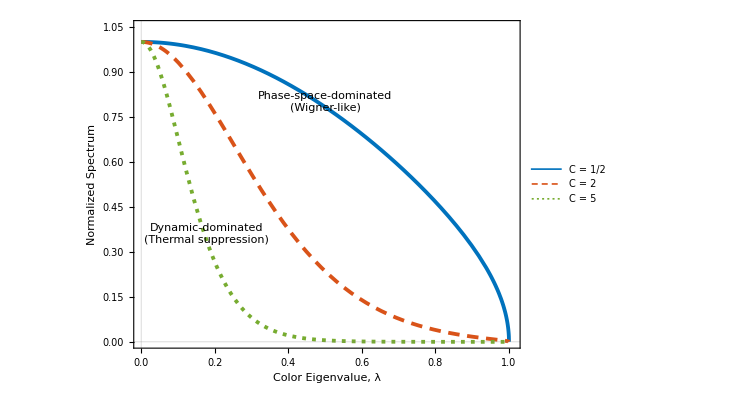

```mathematica
paperPlot=Plot[Evaluate[normalizedFunctions],{λ,0,1},(*Aesthetics and Framing*)PlotTheme->"Scientific",Frame->True,FrameLabel->{Style["Color Eigenvalue, λ",FontSize->18],Style["Normalized Spectrum",FontSize->18]},FrameTicksStyle->Directive[Black,16],PlotRange->{{0,1.01},{0,1.05}},ImageSize->550,AspectRatio->3/4,PlotStyle->Transpose[{plotColors,plotStyles}],PlotLegends->Placed[LineLegend["C = "<>ToString[#,TraditionalForm]&/@Rationalize[cValues],LegendFunction->(Framed[#,RoundingRadius->4,Background->White]&),LegendMarkerSize->30,LabelStyle->{FontSize->18}],{0.85,0.75} ],Epilog->{Text[Framed[Style["Phase-space-dominated\n(Wigner-like)",16,Black],Background->Opacity[1,White],FrameStyle->None,RoundingRadius->3],{0.5,0.8}],Text[Framed[Style["Dynamic-dominated\n(Thermal suppression)",16,Black],Background->Opacity[1,White],FrameStyle->None,RoundingRadius->3],{0.178,0.36}]}]
```

```mathematica
Export["./rootThermalityPlot.pdf",paperPlot]
```

./rootThermalityPlot.pdf